```mathematica
ma=6.015122;
mi=170.936323;
```

We need to develop an angular grid from θ_1 to θ_2 that varies smoothly with R.  We want the grid to concentrate points at θ_1 and θ_2 when R≫R_0 but distribute the points approximately uniformly when R≪R_0.

To warm up let’s write some subroutines for simple grids.

A linear grid:

```mathematica
LinearGrid[x1_,x2_,NPTS_]:=Module[{dx},
dx=(x2-x1)/(NPTS-1);
Table[x1+(i-1)dx,{i,1,NPTS}]
]
```

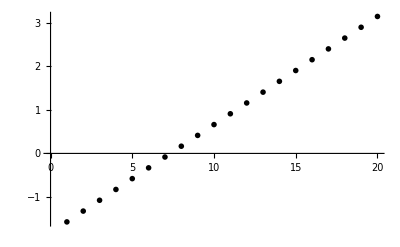

```mathematica
ListPlot[LinearGrid[-π/2,π,20]]
```

A quadratic grid will concentrate points near x_1

```mathematica
QuadraticGrid[x1_,x2_,NPTS_]:=Module[{Δx},
Δx=(x2-x1);
Table[x1+((i-1)/(NPTS-1))^2 Δx,{i,1,NPTS}]
]
```

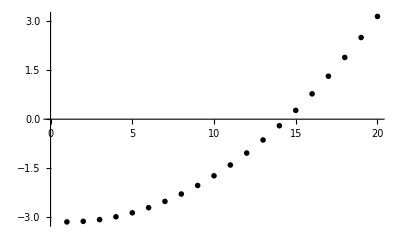

```mathematica
ListPlot[QuadraticGrid[-π,π,20]]
```

Perhaps the following arctangent function?

```mathematica
ArcTanGrid[x1_,x2_,NPTS_,R0_,R_]:=Module[{Δx,xScale,res},
Δx=(x2-x1);
res=Table[(ArcTan[(((i-1)/(NPTS-1))-1/2)R/R0]/(2ArcTan[(1/2)R/R0]))Δx,{i,1,NPTS}];
res
]
```

```mathematica
ArcTanGrid[-10,10,20.,1,10]
```

{-10.,-9.83604,-9.63071,-9.36661,-9.01541,-8.52833,-7.81603,-6.70544,-4.86595,-1.87362,1.87362,4.86595,6.70544,7.81603,8.52833,9.01541,9.36661,9.63071,9.83604,10.}

```mathematica
Manipulate[ListPlot[ArcTanGrid[-10,10,100,1,R],GridLines->Automatic,Frame->True],{R,.01,10}]
```

```mathematica
Simplify[Solve[{Ne ψ1==Cos[kx1]-Tandel Sin[kx1],Ne ψ2== Cos[kx2]-Tandel Sin[kx2]},{Ne,Tandel}]]
```

{{Ne→Sin[kx1-kx2]/(ψ2 Sin[kx1]-ψ1 Sin[kx2]),Tandel→(ψ2 Cos[kx1]-ψ1 Cos[kx2])/(ψ2 Sin[kx1]-ψ1 Sin[kx2])}}

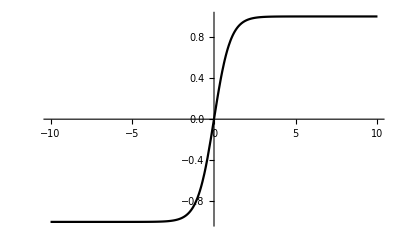

```mathematica
Plot[Tanh[x],{x,-10,10}]
```

```mathematica
TanhGrid[x1_,x2_,NPTS_,R0_,R_]:=Module[{Δx,xScale,res},
Δx=(x2-x1);
res=Table[(Tanh[(((i-1)/(NPTS-1))-1/2)R/R0]/(2Tanh[(1/2)R/R0]))Δx,{i,1,NPTS}];
res
]
```

```mathematica
Manipulate[ListPlot[{ArcTanGrid[-10,10,100,1,R],TanhGrid[-10,10,100,1,R]},GridLines->Automatic,Frame->True,PlotStyle->{Black,Red}],{R,.01,10}]
```

If we want to have another concentration of points near the center, we might try (from Nick S.’s suggestion) a function like x-sin(x)

```mathematica
ma=6.015122 ;
mi=170.936323 ;
μ=Sqrt[ma/mi]
```

0.187588

```mathematica
θc=ArcTan[μ]
```

0.185433

```mathematica
f[a_,x_]:=a 4π x-Sin[4π x];
```

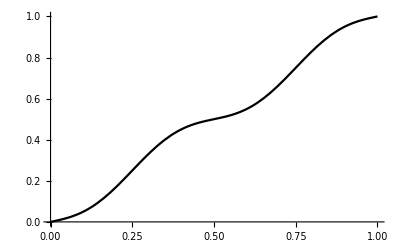

```mathematica
Plot[f[1.5,x]/f[1.5,1],{x,0,1}]
```

```mathematica
xminusSinxGrid[x1_,x2_,NPTS_,R0_,R_]:=Module[{Δx,xScale,res},
Δx=(x2-x1);
res=Table[x1+(f[Exp[Max[R0/R,.75]],(((i-1)/(NPTS-1)))]/f[Exp[Max[R0/R,.75]],1])Δx,{i,1,NPTS}];
res
]
```

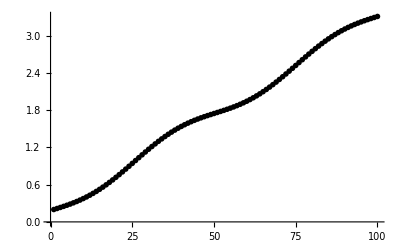

```mathematica
ListPlot[xminusSinxGrid[0.19957640207132948,3.3128821615638451,100,10.259993539726262,50.0]]
```

```mathematica
R0=20;Manipulate[ListPlot[xminusSinxGrid[-10,10,100,R0,R],GridLines->Automatic,Frame->True, Epilog->{Text["R0/R = ",{20,2.2}],Text[R0/R,{35,2.2}]}],{R,.1,100}]
```

```mathematica
Manipulate[ListPlot[{ArcTanGrid[-10,10,100,1,R],TanhGrid[-10,10,100,1,R],xminusSinxGrid[-10,10,100,R0,R]},GridLines->Automatic,Frame->True,PlotStyle->{Black,Red,Blue}],{R,.01,10}]
```

### Center-of-mass and relative coordinates for the atom-ion problem

How do we determine the laplacian under general coordinate transformations?

Let’s define a coordinate transformation from a set of coordinates x⃗ to y⃗ as:

y⃗=S x⃗

so that

y_i=∑_j S_ij x_j

For a function f({y_i({x_j})}) we have by the chain rule:

(∂f)/(∂x_j)=∑_i (∂y_i)/(∂x_j)(∂f)/(∂y_i)

Another derivative gives:

(∂^2 f)/(∂x_j^2)=∂/(∂x_j)∑_i ((∂y_i)/(∂x_j)(∂f)/(∂y_i))

(∂^2 f)/(∂x_j^2)=∑_i ((∂/(∂x_j)(∂y_i)/(∂x_j))((∂f)/(∂y_i))+((∂y_i)/(∂x_j))(∂/(∂x_j)(∂f)/(∂y_i)))

(∂^2 f)/(∂x_j^2)=∑_i ((∂/(∂x_j)(∂y_i)/(∂x_j))((∂f)/(∂y_i))+((∂y_i)/(∂x_j))(∑_k (∂y_k)/(∂x_j)∂/(∂y_k)(∂f)/(∂y_i)))

(∂^2 f)/(∂x_j^2)=∑_i (((∂^2 y_i)/(∂x_j∂x_j))((∂f)/(∂y_i))+((∂y_i)/(∂x_j))(∑_k (∂y_k)/(∂x_j)∂/(∂y_k)(∂f)/(∂y_i)))

This formula is quite general and the derivatives can be expressed in terms of the matrix elements S_ij.  Now if the matrix elements S_ij are constants (as is the case for the transformation to Jacobi coordinates) then all second derivatives (∂^2 y_i)/(∂x_j∂x_j)=0, and we are left with:

∂^2/(∂x_j^2)=∑_i ∑_k ((∂y_i)/(∂x_j)(∂y_k)/(∂x_j)∂/(∂y_k)∂/(∂y_i))=∑_i ∑_k (S_ij S_kj∂/(∂y_k)∂/(∂y_i))

∂^2/(∂x_j^2)=∑_i (S_ij∂/(∂y_i))∑_k (S_kj∂/(∂y_k))

∑_j 1/(2 m_j)∂^2/(∂x_j^2)=∑_j 1/(2 m_j){∑_i (S_ij∂/(∂y_i))∑_k (S_kj∂/(∂y_k))}

### Mass-Scaled Jacobi coordinates

```mathematica
Clear[μ]
```

For converting to mass-scaled Jacobi coordinates, the transformation matrix S is defined as:

S=1/(√μ)U M^(1/2)

where M^(1/2) and U are defined as:

(J.B. McGuire, J. Math Phys. 5, 622 (1964))

```mathematica
MrootMat[NN_]:=Table[If[i==j,√Subscript[m, i],0],{i,1,NN},{j,1,NN}];
Umat[NN_]:=Simplify[Table[Which[i>n+1,0,n==NN,(√Subscript[m, i])/(√Sum[Subscript[m, j],{j,1,NN}]),n≥i&&n<NN,(√(Subscript[m, n+1] Subscript[m, i]))/(√Sum[Subscript[m, j],{j,1,n+1}] √Sum[Subscript[m, j],{j,1,n}]),i==n+1&&n<NN,(-√Sum[Subscript[m, j],{j,1,n}])/(√Sum[Subscript[m, j],{j,1,n+1}])],{n,1,NN},{i,1,NN}],Table[Subscript[m, i]>0,{i,1,NN}]];
```

```mathematica
S[NN_]:=1/(√μ)FullSimplify[Umat[NN].MrootMat[NN],Table[Subscript[m, i]>0,{i,1,NN}]]
```

```mathematica
MatrixForm[S[2]]
```

((√((m_1 m_2)/(m_1+m_2)))/(√μ) | -(√((m_1 m_2)/(m_1+m_2)))/(√μ)
m_1/(√μ √(m_1+m_2)) | m_2/(√μ √(m_1+m_2)))

```mathematica
MatrixForm[S[3]]
```

((√((m_1 m_2)/(m_1+m_2)))/(√μ) | -(√((m_1 m_2)/(m_1+m_2)))/(√μ) | 0
(m_1 √(m_3/((m_1+m_2) (m_1+m_2+m_3))))/(√μ) | (m_2 √(m_3/((m_1+m_2) (m_1+m_2+m_3))))/(√μ) | -(√(((m_1+m_2) m_3)/(m_1+m_2+m_3)))/(√μ)
m_1/(√μ √(m_1+m_2+m_3)) | m_2/(√μ √(m_1+m_2+m_3)) | m_3/(√μ √(m_1+m_2+m_3)))

```mathematica
MatrixForm[MrootMat[2]/.{Subscript[m, 1]->1,Subscript[m, 2]->μ^2}]
```

(1 | 0
0 | √(μ^2))

```mathematica
SS=Simplify[S[2]/.{Subscript[m, 1]->1,Subscript[m, 2]->μ^2}]
```

{{(√(μ^2/(1+μ^2)))/(√μ),-(√(μ^2/(1+μ^2)))/(√μ)},{1/(√μ √(1+μ^2)),μ^(3/2)/(√(1+μ^2))}}

```mathematica
MatrixForm[Simplify[Umat[2]/.{Subscript[m, 1]->1,Subscript[m, 2]->μ^2}]]
```

(√(μ^2/(1+μ^2)) | -√(1/(1+μ^2))
√(1/(1+μ^2)) | √(μ^2/(1+μ^2)))

```mathematica
FullSimplify[Sum[1/(2 Subscript[m, j])SS[[k]][[j]]SS[[i]][[j]]p[k]p[i](*/.{μ12->(Subscript[m, 1] Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2]),μ123->((Subscript[m, 1]+Subscript[m, 2])Subscript[m, 3])/(Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]),M->Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]}*),{k,1,2},{i,1,2},{j,1,2}]/.{Subscript[m, 1]->1,Subscript[m, 2]->μ^2},{μ>0}]
```

(p[1]^2+p[2]^2)/(2 μ)

```mathematica
FullSimplify[SS,μ>0]//MatrixForm
```

(1/(√(1/μ+μ)) | -√(μ/(1+μ^2))
1/(√(μ+μ^3)) | μ^(3/2)/(√(1+μ^2)))

```mathematica
FullSimplify[Inverse[FullSimplify[SS,μ>0]],μ>0]//MatrixForm
```

(μ^(3/2)/(√(1+μ^2)) | √(μ/(1+μ^2))
-1/(√(μ+μ^3)) | √(μ/(1+μ^2)))

```mathematica
Clear[μ,mi,ma]
```

```mathematica
invtrans=Collect[Simplify[Solve[({{u}, {v}})==1/(√(μ(1+μ^2)))({{√μ μ, -μ/√μ}, {√μ, μ^2/√μ}}).({{x}, {y}}),{x,y}],μ>0],{u,v}]
```

{{x→v/(√(1+μ^2))+(u μ)/(√(1+μ^2)),y→-u/(√(1+μ^2))+(v μ)/(√(1+μ^2))}}

```mathematica
Collect[μ x^2/.invtrans,{u,v}]
```

{(v^2 μ)/(1+μ^2)+(2 u v μ^2)/(1+μ^2)+(u^2 μ^3)/(1+μ^2)}

```mathematica
FullSimplify[1/(√μ x-y/(√μ))^4/.invtrans]
```

{μ^2/(u^4 (1+μ^2)^2)}

```mathematica
FullSimplify[√μ x-y/(√μ)/.invtrans]
```

{(u √(1+μ^2))/(√μ)}

```mathematica
FullSimplify[Det[1/(√(μ(1+μ^2)))({{√μ μ, -μ/√μ}, {√μ, μ^2/√μ}})]]
```

1

```mathematica
FullSimplify[μ (x^2+y^2)/.%]
```

{(2 v^2 μ^2+2 u v μ (-1+μ^2)+u^2 (1+μ^4))/(1+μ^2)}

```mathematica
FullSimplify[(μ^2-1)μ/(1+μ^2)/.μ->Tan[θ]]
```

-Cos[2 θ] Tan[θ]